## Import

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"negf.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

```mathematica
GetOrbitalΣ[Σd_]:=Module[{},
bands=(
{atomIndex,σ}=#;
Band[{orbInForAtomIn[[atomIndex]],orbInForAtomIn[[atomIndex]]}]->
σ*IdentityMatrix[MAXORB[types⟦atomIndex⟧]]
)&/@Σd;
SparseArray[bands,{norb,norb}]
]
```

## Ham gen

```mathematica
moleName="CNB_Au";
{atoms,types,bonds}=ImportXYZ[moleName<>".xyz"];
```

```mathematica
h=DFTBSolver2[atoms,types];
s=DFTBSolver2[atoms,types,"S"];
```

```mathematica
Export[moleName<>".h.mx",h];
Export[moleName<>".s.mx",s];
```

```mathematica
AUE=Quantity["HartreeEnergy"/"Electronvolts"]//UnitConvert
```

27.211386246

```mathematica
atomsM=atoms⟦;;68⟧;
typesM=types⟦;;68⟧;
hM=DFTBSolver2[atomsM,typesM];
sM=DFTBSolver2[atomsM,typesM,"S"];
{eval,evec}=MyEigensystem[{hM,sM}];
```

```mathematica
h//Dimensions
```

{1254,1254}

```mathematica
{coords,types,bonds}=ImportXYZ[moleName<>".xyz"];
```

```mathematica
raw["self.energy"]=Import[moleName<>".self.energy.in","Table"]⟦2;;-2⟧;
(*self energy diagonal element: atom index, Im self energy[Hartree]*)
ΣdL=Select[raw["self.energy"],#⟦-2⟧=="left"&]⟦All,{1,-1}⟧;
ΣdR=Select[raw["self.energy"],#⟦-2⟧=="right"&]⟦All,{1,-1}⟧;
(*orbital-atom relation*)
orbInAtom=MAXORB/@types;
norb=Total[MAXORB/@types];
orbInForAtomIn=Accumulate[{1}~Join~orbInAtom][[1;;-2]];
(*self energy diagonal element applied to orbital: orbital index, Im self energy[Hartree]*)
ΣL=-I*AUE*GetOrbitalΣ[ΣdL];
ΣR=-I*AUE*GetOrbitalΣ[ΣdR];
```

```mathematica
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atomsM,typesM];
EF
```

-4.54151

## NEGF run

```mathematica
{emin,emax,estep}={EF-2,EF+2,0.1};
```

```mathematica
et=Table[
{ϵ-EF,NEGFSystemWBΣS[ϵ,h,s,ΣL,ΣR]⟦1⟧},
{ϵ,emin,emax,estep}
]
```

{{-2.,0.965799},{-1.9,1.04563},{-1.8,1.14235},{-1.7,1.39285},{-1.6,1.13723},{-1.5,0.808056},{-1.4,0.722067},{-1.3,0.805801},{-1.2,0.520372},{-1.1,0.584815},{-1.,0.992155},{-0.9,0.51373},{-0.8,0.158799},{-0.7,0.0634112},{-0.6,0.0316392},{-0.5,0.0184732},{-0.4,0.0121284},{-0.3,0.00873779},{-0.2,0.00679759},{-0.1,0.00564937},{0.,0.00498781},{0.1,0.0046842},{0.2,0.00472933},{0.3,0.00524226},{0.4,0.00655681},{0.5,0.00949088},{0.6,0.0161885},{0.7,0.03311},{0.8,0.0837223},{0.9,0.269756},{1.,0.833375},{1.1,0.913049},{1.2,0.66479},{1.3,0.589467},{1.4,0.627445},{1.5,0.746567},{1.6,0.944598},{1.7,1.21591},{1.8,1.17928},{1.9,1.07269},{2.,1.11772}}

```mathematica
etExt=Import["CNB_Au.TE.ext.dat","Data"]⟦4;;-2,2;;3⟧;
```

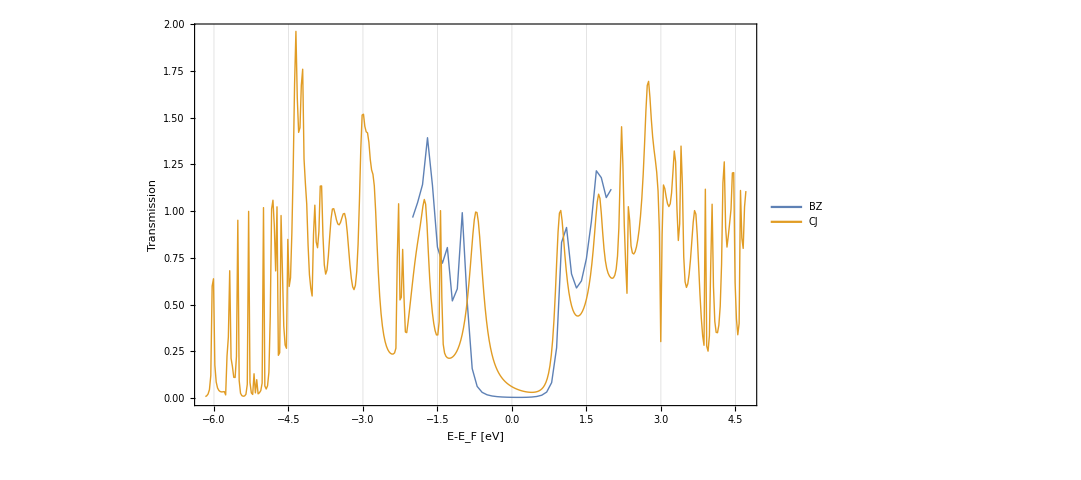

```mathematica
ListPlot[{et,etExt},GridLines->{eval-EF,None},
FrameLabel->{"E-E_F [eV]"," Transmission "},
Frame->True,
AspectRatio->0.6,
PlotLegends->Placed[{"BZ","CJ"},{0.55,0.8}],
Joined->True,
PlotStyle->Thick,
ImageSize->{800,500},
Axes->False,
styles]
```